```mathematica
MyList[n_,p_]:=ReadList[StringJoin["d:\\Triangle\\Data\\",ToString[n],"_",ToString[p],".txt"],Number]
```

```mathematica
ShortList[n_,p_] := Select[ MyList[n,p], # < 10^30&]
```

```mathematica
T:=Table[ Length[MyList[n, Prime[p]]], {p,3,6,1},{n,3,4,1}]
```

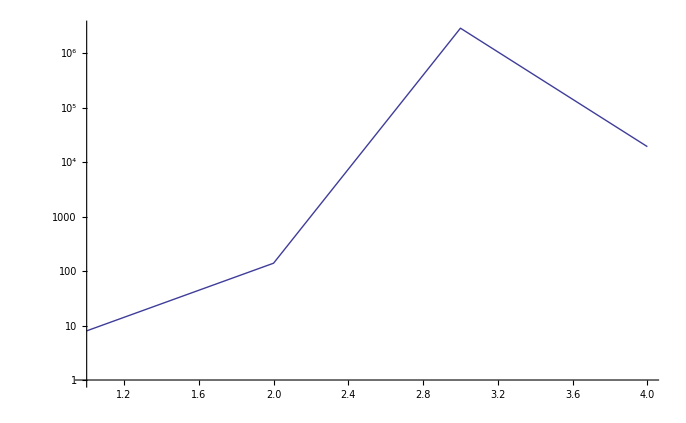

```mathematica
ListLogPlot[Flatten[T], Joined->True]
```

```mathematica
T
```

{{8},{140},{2911726},{19394}}

```mathematica
ListLogPlot[Table[Length[MyList[n, 11]], {n,50,1}], Joined->True]
```

ListLogPlot::argx: ListLogPlot called with 0 arguments; 1 argument is expected.

```mathematica
ShortList[4,3]
```

{0,1,3160}

ReadList::nffil: File not found during ReadList[.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 < 10^30 &].

ReadList::nffil: File not found during ReadList[.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 < 10^30 &].

ReadList::nffil: File not found during ReadList[.

General::stop: Further output of ReadList will be suppressed during this calculation.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 < 10^30 &].

General::stop: Further output of Select will be suppressed during this calculation.

{{135,101976,13887783,1137203,2,2},{3,8,76,714,19394,2},{2,5,12,7,13,2},{2,4,5,6,6,2},{2,4,8,6,14,18},{2,3,4,6,7,9},{2,3,4,6,7,9},{2,3,4,6,7,9}}

```mathematica
ListLogLogPlot[MyList[3,7], Joined->True]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
ListPlot3D[Table[Length[ShortList[n, p]], {n,3,10,1},{p,{3,5,7,11}}]]
```

-Graphics3D-